{0.00424391,{t→379.585}}

379.585

0.00424391

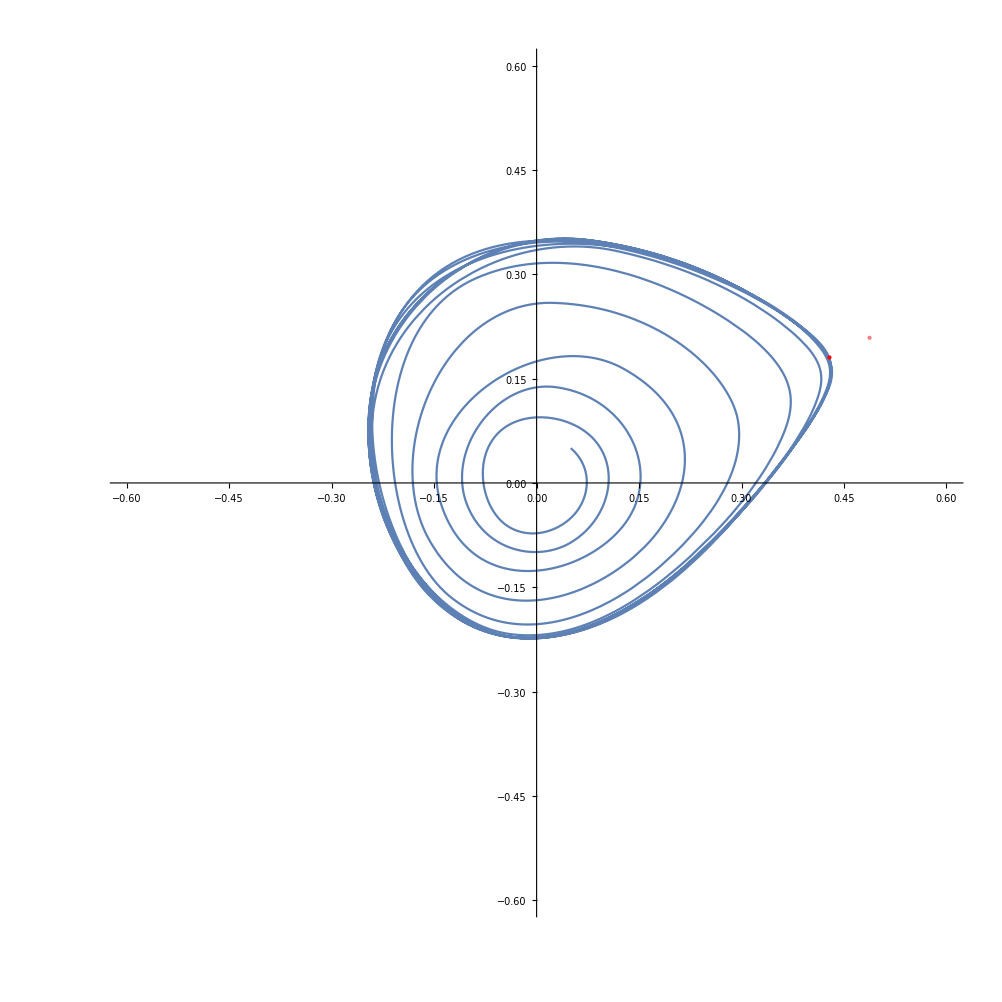

```mathematica
Clear["Global`*"]
tMax = 1000;
μ = 0.059;
sol:=NDSolve[{x'[t]== μ*x[t] + y[t] - x[t]^2,y'[t]==-x[t] + μ*y[t] + 2*x[t]^2,x[0]==0.05,y[0]==0.05},{x,y},{t,tMax}, Method->"StiffnessSwitching"]
xStar = (μ^2+1)/(μ+2);
yStar = xStar^2 - μ*xStar;

distance[t_] = (((x[t]/.sol[[1]])-xStar)^2 + ((y[t]/.sol[[1]])-yStar)^2);

min = Minimize[{(((x[t]/.sol[[1]])-xStar)^2 + ((y[t]/.sol[[1]])-yStar)^2),0 < t<tMax}, t]
tMin = t/.min[[2]]
distance[tMin]

Show[
ParametricPlot[Evaluate[{x[t],y[t]}/.sol], {t,0,100}, PlotRange ->{-0.6, 0.6}],
Graphics[{PointSize[Large], Pink, Point[{xStar,yStar}]}],
Graphics[{PointSize[Large], Red,Point[{x[tMin]/.sol[[1]], y[tMin]/.sol[[1]]}]}]
]
```

```mathematica
NumberForm[0.0011047251580382628,16]
```

0.001104725158038263

```mathematica
NumberForm[0.0004359074464754355,16]
```

0.0004359074464754355

```mathematica
NumberForm[0.0004359074464754355,16]
```

0.0004359074464754355

```mathematica
distance[t/.min[[2]]]
```

0.0489753